```mathematica
Quit[]
```

# Biofilm model

## Fennie van der Graaf, Jelle molenkamp & Ronja Hulst Team RootPatch iGEM Groningen How it works: use “Shift -Enter “ to run the code, start with the running the Quit[] to clear previous calculations. you can drop down the code and the plots with the button after the orange text, and see/ run the code and the plots. the introduction, the model and conclusion/discussion does not contain any code. the first part of our code is under “results” “outcome”. this This part needs to be executed before you can run the code in the “analysis “section. the code is linked and it only works if you run all of it. in the analysis are the bifurcation plots.

## Table of contents

Introduction
The model
Results
Analysis
Conclusion /discussion

## Introduction

For the rootpatch to work properly a sufficient amount of NLP has to be produced. the amount of NLP produced. The amount of bacteria surviving in the soil is directly related to how much NLP they produce. Which is the reason to make a model of the population of our model.
In soil there are a lot of different factors that influence the growth of bacteria.
-Graphics-Figure 1: Influences on population of our GMO

we need to think about competition with other bacteria. the temperature and soil humidity. and the maximum carrying capacity for bacteria near the root. 
We did some research on the temperature in the soil and with this we could make an equation for the temperature in the soil over time. the equation for the temperature from the start of the season (here time = 0) to about 200 days after (end potato season) is:
temperature = 4.75+14.09*Sin[0.01057*t+0.3018]
-Graphics-Figure 2: Data from KMNI for soil temperature

The same thing should be done for the moisture, but the soil is measured in moisture content and the growth of bacteria with water activity. The relation between soil moisture and water activity changes with the soil type. 
More about this.....

Also the area close to the root has a maximum for the amount of bacteria that can be in close porximity. Some of these bacteria will migrate further away from the plant to the soil. In the soil is a lot more space for the bacteria to live, but there are less nutrients. Our GMO carries a killswitch, which means the bacteria will die if it is not close enough to the roots. 

This model is to figure out how robust the GMO will be throughout the potato growing season, and thus if it will produce a sufficient amount of NLP to chase away G. pallida.

## The Model

We made a system of ODE to represent the bacterial population over time. We took two different bacteria in this model, Our GMO and the Non-GMO counterpart of this bacteria that is already in the soil (B.mycoeids).
 
 the growth rate equation of the population was taken from the already existing Ratkowksy sqaure root equation. In this equation the growth of the bacteria is dependent on the temperature (T) , the minimum temperature for the bacteria to survive (Tmin), the wateractivity (Aw), and the minumum wateractivity (AWmin). the growth equation for the model looks like this:
-Graphics-
To represent the migration from the plant to the soil and back, patches were created for each bacteria. the bacteria can be near the root and further away from the root. Transfer between the area’s is labeled patch transfer and implemented in the model as these equations:
-Graphics-Figure: Patch transfer from and to the roots.
These equations are a part of the entire population equations. The system of ODEs for the model consist of 4 population ODEs, one for the GMO near the root (G), one for the GMO in the soil (M), one for the Wild type bacteria (B), and one for the Wild type bacteria in the soil (A). the competition between the species is modelled with a competition coefficient. The kill switch is implemented as a rate at which the bacteria die in the soil.
-Graphics-Figure: population equations

## Results

## Outcome

Implementing the model with it’s parameters you can see a clear plot with the bacterial population over time, where t=0 is the start of the potato growing season. the maximum carrying capacity in the soil is 5 times larger than the carrying capacity near the roots because there is more space. The population plot will look something like this:

```mathematica
f[a0p_,b0p_,d1p_,dp_,Ap_,tp_,sp_]:=Module[{a0=a0p,b0=b0p,d1=d1p,d=dp,Amin=Ap,tmin=tp,s=sp},
Kill=10;
Sp=1000;
Ss=3000;

T[t_]:=4.75+14.09*Sin[0.01057*t+0.3018];
Aw[t_]:=0.97+0.0001*t;
Growth[t_]:=((T[t]-tmin)^2*(Aw[t]-Amin));
Growth2[t_]:=0.5*((T[t]-tmin)^2*(Aw[t]-Amin));
S[t_]:=G[t]*s*((G[t]+a0*B[t])/Sp)+G[t]*d;
P[t_]:=M[t]*d1;
P2[t_]:=A[t]*d1;
S2[t_]:=B[t]*s*((B[t]+b0*G[t])/Sp)+B[t]*d;

GMOp=G'[t]==Growth[t]*G[t]*((Sp-G[t]-a0*B[t])/Sp)+P[t]-S[t];
GMOs=M'[t]==(Growth2[t]-Kill)*M[t]*((Ss-M[t]-a0*A[t])/Ss)+S[t]-P[t];Wildp=B'[t]==Growth[t]*B[t]*((Sp-B[t]-b0*G[t])/Sp)+P2[t]-S2[t];Wilds=A'[t]==Growth2[t]*A[t]*((Ss-A[t]-b0*M[t])/Ss)+S2[t]-P2[t];

all={GMOp,GMOs,Wildp,Wilds};
init1={G[0]==500,M[0]==5,B[0]==500,A[0]==2000};
tmax=200;
Solution=NDSolveValue[{all,init1},{G[t],M[t],B[t],A[t]},{t,0,tmax}];

Solution]
sol=f[.4,.5,.1,.01,.95,9,0.01];
Plot[sol,{t,0,190},FrameTicksStyle->Directive[FontSize->16],PlotStyle->{Purple,Blue, Green,Orange},PlotLabels->{Style["GMOp    ",FontSize->13],Style["GMOs    ",FontSize->13], Style["WTp    ",FontSize->13],Style["WTs    ",FontSize->13]}, PlotLabel->Style["Bacteria populations over time",FontSize -> 25],Frame->{True,True,False,False},FrameLabel->{Style["Time (Days) ",FontSize->18],Style["Population",FontSize->18]},PlotRange->{0,3000}]
```

-Graphics-

The GMO has a stable population size of about 50% of the maximum carrying capacity.

## Manipulation

Some of the parameters don’t have a known value, because it could not be tested in the lab becuase of corona. To get a feeling of how the parameters influence the outcome of the bacterial populations a manipulate plot was made:

```mathematica
RunBacteria[a0_,b0_,d_,d1_,s_,Tmin_,Awmin_,G0_,M0_,B0_,A0_]:=
Module[{ToPlant, ToSoil, ToPlant2, ToSoil2, Growth, Growth2, eq1, eq2,eq3,eq4,Solution,T,Aw,all,initS,Ssoil,Splant},
ToPlant:= M[t]* d1 ;
ToSoil := G[t]*s*((G[t] +a0*B[t])/Splant)+G[t]*d     ;
ToPlant2 := A[t]* d1;
ToSoil2:= B[t]*s*((B[t]+b0*G[t])/Splant) +B[t]*d;
Growth = ((T-Tmin)^2*(Aw-Awmin))  ;  (*Growth  near root*)
Growth2 = 0.5*((T-Tmin)^2*(Aw-Awmin));(*Growth in bulk soil*)
T=4.75+14.09*Sin[0.01057*t+0.3018];
Aw=0.97+0.0001*t;
(*ODEs*)
eq1 = D[G[t],t]==Growth*G[t]*((Splant-G[t] -a0*B[t])/Splant)+ToPlant-ToSoil;
eq2 = D[M[t],t]==  (Growth2-10)*M[t]*((Ssoil-M[t]-a0*A[t])/Ssoil)+ToSoil-ToPlant ;
eq3 = D[B[t],t] == Growth*B[t]*((Splant-B[t]-b0*G[t])/Splant) +ToPlant2-ToSoil2;
eq4 = D[A[t],t]== Growth2* A[t]*((Ssoil- A[t]-b0*M[t])/Ssoil)+ToSoil2-ToPlant2; 
(*Solve*)
Ssoil=5000;
Splant=1000;

all = { eq1,eq2,eq3,eq4};  (* system of ODEs*)
initS = {G[0]==G0,M[0]==M0,B[0]==B0,A[0]==A0};
Solution = NDSolveValue[{all,initS},{G[t],M[t],B[t],A[t]},{t,0,200}];  (*solution for system of ODEs*)

Plot[Solution,{t,0,200},PlotStyle->{Red,Orange,Green,Yellow}, PlotLabels->{"GMO-plant", "GMO-soil", "WT-plant", "WT-soil"}, PlotLabel->"Bacteria populations", PlotRange->All]]
Manipulate[RunBacteria[a0, b0,d, d1, s, Tmin, Awmin, G0, M0, B0, A0],

{{a0, 0.5, "comp WT"}, 0, 1, 0.1, Appearance -> "Labeled", ImageSize-> Tiny},
{{b0, 0.5, "comp GMO"}, 0, 1, 0.1, Appearance -> "Labeled", ImageSize-> Tiny},
{{d, 0.1, "Pdif to bulk"}, 0, 1, 0.1, Appearance -> "Labeled", ImageSize-> Tiny},
{{d1, 0.1, "Pdif to plant"}, 0, 1, 0.1, Appearance -> "Labeled", ImageSize-> Tiny},
{{s, 0.001, "Adif to bulk"}, 0, 0.2, 0.01, Appearance -> "Labeled", ImageSize-> Tiny},
{{Tmin, 12, "minimum temp"}, 10, 15, 1, Appearance -> "Labeled", ImageSize-> Tiny},
{{Awmin,0.93 , "min. water activity"}, 0.93, 0.99, 0.01, Appearance -> "Labeled", ImageSize-> Tiny}, 
Delimiter, 
{{G0,1000 , "G[0]"}, 0, 10000, 500, Appearance -> "Labeled", ImageSize-> Tiny},
{{M0,1000 , "M[0]"}, 0, 10000, 500, Appearance -> "Labeled", ImageSize-> Tiny},
{{B0,1000 , "B[0]"}, 0, 10000, 500, Appearance -> "Labeled", ImageSize-> Tiny},
{{A0,1000 , "A[0]"}, 0, 10000, 500, Appearance -> "Labeled", ImageSize-> Tiny}
]
```

## Analysis

Because the exact values of the parameters could not be determined, we analyzed each parameter and the outcome it has on the model on the beginning of the season (after 30 days) and around the end of the season (150 days).
The NLP production is most needed at the end of the season.

### Minimum Temperature

It is known that for B. mycoides the minimal temperature required for growth is somewhere in between 10 and 15 degrees. we look at the outcome of the model for these values of the min. temperature and see how much impact it has on the end population at t = 150 and at the population at the beginning t = 30.

```mathematica
solpT[tp_]:=f[.4,0.5,.1,.01,.95,tp,0.01]/.t->150;
solpT2[tp_]:=f[.4,0.5,.1,.01,.95,tp,0.01]/.t->30;
var={G,M,B,A};

Plot[{solpT2[tp][[1]],solpT2[tp][[2]],solpT2[tp][[3]],solpT2[tp][[4]]},{tp,5,12},Frame->{True,True,False,False},FrameLabel->{Style["Minimum temperature (°C) ",FontSize->18],Style["Population",FontSize->18]},PlotLabel->Style["Minimal growth temperatures(t=30)",FontSize->20],FrameTicksStyle->Directive[FontSize->16],PlotStyle->{Purple,Blue, Green,Orange},PlotLabels->{Style["GMOp    ",FontSize->13],Style["GMOs    ",FontSize->13], Style["WTp    ",FontSize->13],Style["WTs    ",FontSize->13]}]

Plot[{solpT[tp][[1]],solpT[tp][[2]],solpT[tp][[3]]},{tp,5,12},Frame->{True,True,False,False},FrameLabel->{Style["Minimum temperature (°C) ",FontSize->18],Style["Population",FontSize->18]},PlotLabel->Style["Bifurcation plot of Minimal growth temperature",FontSize->20],FrameTicksStyle->Directive[FontSize->16],PlotStyle->{Purple,Blue, Green,Orange},PlotLabels->{Style["GMOp    ",FontSize->13],Style["GMOs    ",FontSize->13], Style["WTp    ",FontSize->13],Style["WTs    ",FontSize->13]}]
```

-Graphics-

-Graphics-

If we look at the outcome for our GMO at three minimum temperatures, (Tmin= 10, Tmin=12.5, and Tmin=15) we get these results:

-Graphics-

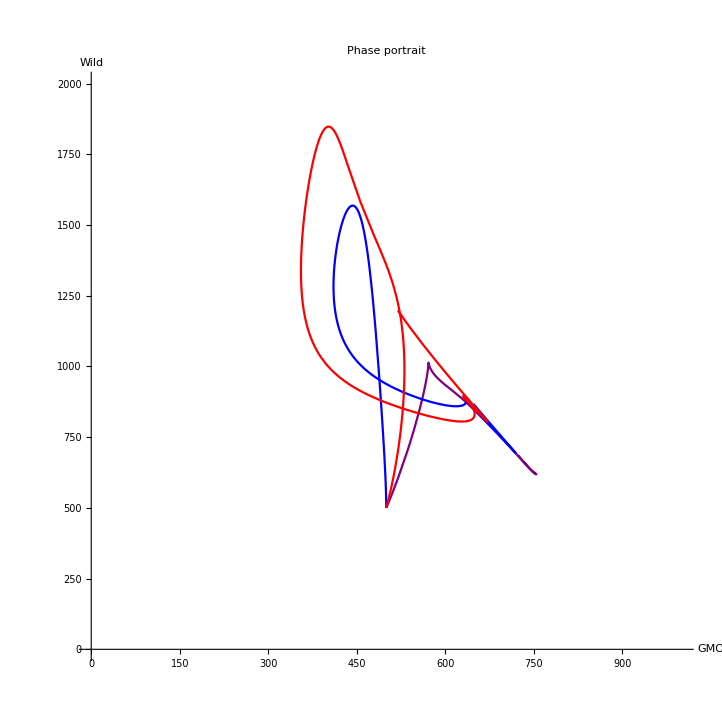

```mathematica
solt1=f[.4,.6,.1,.01,.95,5,0.001];
solt2=f[.4,.6,.1,.01,.95,9,0.001];
solt3=f[.4,.6,.1,.01,.95,12,0.001];
Plot[{solt1[[1]],solt2[[1]],solt3[[1]]},{t,0,200},PlotStyle->{Purple,Magenta,Pink},PlotLabels->{"10 °C", "12 °C", "15 °C"}, PlotLabel->"Different Minimal temperature",AxesLabel -> {"t", "N"}]
Show[ParametricPlot[{{solt1[[1]],solt1[[3]]},{solt2[[1]],solt2[[3]]},{solt3[[1]],solt3[[3]]}},{t,0,200},PlotRange->{{0,1000},{0,2000}},PlotStyle->{Purple,Blue,Red},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"GMO","Wild"}],StreamPlot [{GMO,Wild},{G,0,20},{B,0,4},StreamScale->{Tiny,Automatic,10}, StreamStyle->Pink]]
```

This plot shows that the bacterial population for tmin= 15 will decline fast in the beginning when the temperatures are low, even though the population is increasing again at a later time. the population is a bit more unstable.

### Minimum water Activity

the minimum water activity for our bacteria is around 0.95, a plot

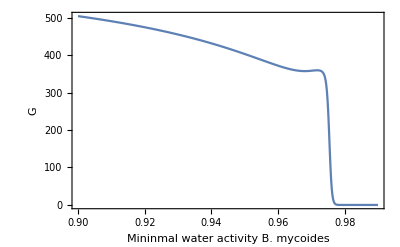
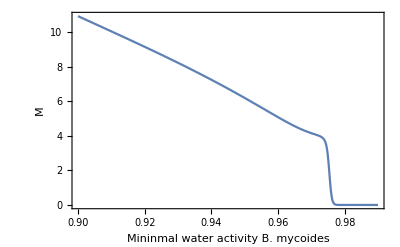
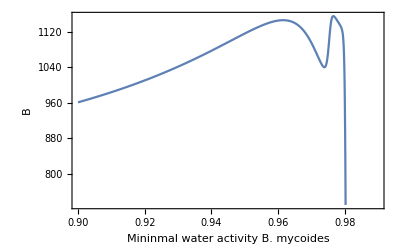
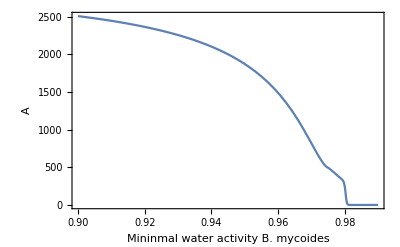

-Graphics-

```mathematica
w[a0p_,b0p_,dp_,d1p_,sp_, Spp_, Ssp_,  Awminp_, Tminp_]:=
Module[{a0=a0p,b0=b0p,d=dp,d1=d1p,s=sp, Splant=Spp, Ssoil=Ssp, Awmin = Awminp, Tmin = Tminp},
Kill=10;

T:=4.75+14.09*Sin[0.01057*t+0.3018];
Aw:=0.97+0.0001*t;
Growth=(T-Tmin)^2*(Aw-Awmin);
Growth2=0.5*(T-Tmin)^2*(Aw-Awmin);

P:=M[t]*d1;
S:=G[t]*s*((G[t]+a0*B[t])/Splant)+G[t]*d;
P2:=A[t]*d1;
S2:=B[t]*s*((B[t]+b0*G[t])/Splant)+B[t]*d;

sp1=D[G[t],t]==Growth*G[t]*((Splant-G[t]-a0*B[t])/Splant)+P-S;
sp2=D[M[t],t]==(Growth2-Kill)*M[t]*((Ssoil-M[t]-a0*A[t])/Ssoil)+S-P;
sp3=D[B[t],t]==Growth*B[t]*((Splant-B[t]-b0*G[t])/Splant)+P2-S2;
sp4=D[A[t],t]==Growth2*A[t]*((Ssoil-A[t]-b0*M[t])/Ssoil)+S2-P2;

all={sp1,sp2,sp3,sp4};
init1={G[0]== 500,M[0]==0,B[0]==500,A[0]==500};
Solution=NDSolveValue[{all,init1},{G[t],M[t],B[t],A[t]},{t,0,200}];
Solution]
solAwminp[Awminp_]:=w[0.5,0.5,0.1,0.5,0.001, 1000, 3000, Awminp, 10]/.t->150;
var={G,M,B,A};
Table[Plot[solAwminp[Awminp][[i]],{Awminp,0.9,0.99},Frame->True,FrameLabel->{"Mininmal water activity B. mycoides",var[[i]]}],{i,4}]
Plot[{solAwminp[Awminp][[1]],solAwminp[Awminp][[2]],solAwminp[Awminp][[3]],solAwminp[Awminp][[4]]},{Awminp,0.9,0.99},Frame->{True,True,False,False},FrameLabel->{Style["Mimimum water activity ",FontSize->18],Style["Population",FontSize->18]},PlotLabel->Style["Bifurcation plot of Minimal Water activity ",FontSize->20],FrameTicksStyle->Directive[FontSize->16],PlotStyle->{Purple,Blue, Green,Orange},PlotLabels->{Style["GMOp    ",FontSize->13],Style["GMOs    ",FontSize->13], Style["WTp    ",FontSize->13],Style["WTs    ",FontSize->13]}]
```

when plotting different water-activities the outcome is:

-Graphics-

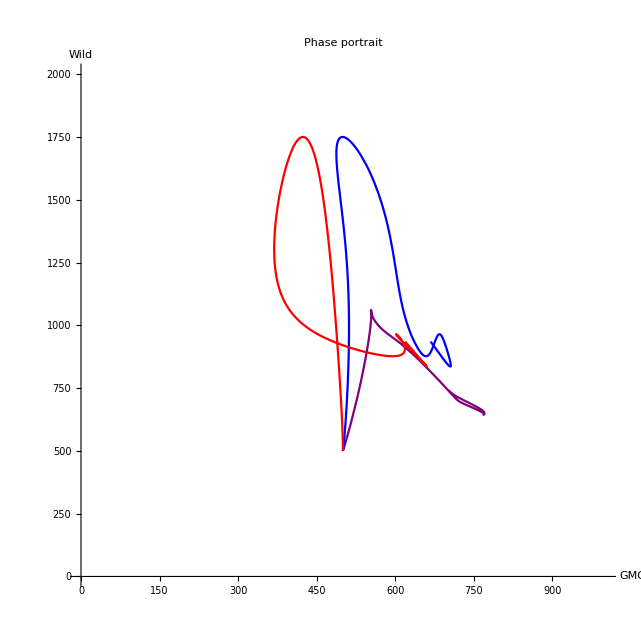

```mathematica
solt4=f[.4,.5,.1,.01,.91,7,0.001];
solt5=f[.4,.5,.1,.01,.95,7,0.001];
solt6=f[.4,.5,.1,.01,.97,7,0.001];
Plot[{solt4[[1]],solt5[[1]],solt6[[1]]},{t,0,200},PlotStyle->{Purple,Magenta,Pink},PlotLabels->{"0.91", "0.95", "0.97"}, PlotLabel->"Different minimal Water activity level",AxesLabel -> {"t", "N"}]
Show[ParametricPlot[{{solt4[[1]],solt4[[3]]},{solt5[[1]],solt6[[3]]},{solt6[[1]],solt6[[3]]}},{t,0,200},PlotRange->{{0,1000},{0,2000}},PlotStyle->{Purple,Blue,Red},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"GMO","Wild"}],StreamPlot [{GMO,Wild},{G,0,20},{B,0,4},StreamScale->{Tiny,Automatic,10}, StreamStyle->Pink]]
```

In these plots you can see clearly that if the Wateractivity in the soil is lower than the minimum wateractivity all bacteria will die.

### Competition

The next parameters to look at are the competition coefficients of the bacteria

#### Competition WT on GMO

the competition of wild type on GMO at t= 150 and t = 30

```mathematica
sola[ap_]:=f[ap,.5,.1,.01,.95,7,0.01]/.t->150;
sola1[ap_]:=f[ap,.5,.1,.01,.95,7,0.01]/.t->30;
Plot[{sola[ap][[1]],sola[ap][[2]],sola[ap][[3]]},{ap,.1,1},Frame->{True,True,False,False},FrameLabel->{Style["Competition Coefficient (Alpha)",FontSize->18],Style["Population",FontSize->18]},PlotLabel->Style["Bifurcation plot of the competition of the WT on the GMO (Alpha)",FontSize->20],FrameTicksStyle->Directive[FontSize->16],PlotStyle->{Purple,Blue, Green,Orange},PlotLabels->{Style["GMOp          .",FontSize->13],Style["GMOs          .",FontSize->13], Style["WTp    ",FontSize->13],Style["WTs    ",FontSize->13]}]
Plot[{sola1[ap][[1]],sola1[ap][[2]],sola1[ap][[3]],sola1[ap][[4]]},{ap,.1,1},PlotStyle->{Purple,Blue, Green, Yellow},Frame->{True,True,False,False},FrameLabel->{"Competition Coefficient","Population after 150 days"},PlotLabel->"Bifurca competition of WildType on GMO (t=30)",PlotLabels->{"GMO-plant","GMO-soil","WT-plant","WT-soil"}]
```

-Graphics-

-Graphics-

over time our population will look like this:

-Graphics-

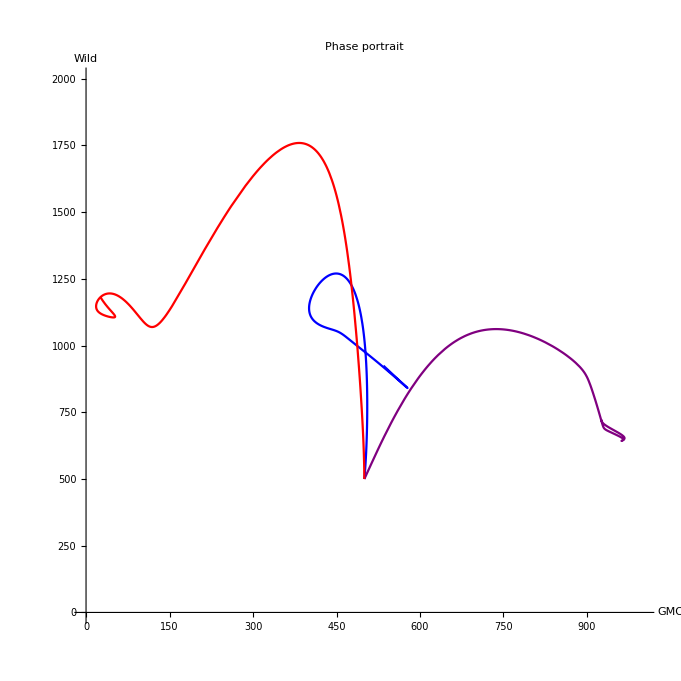

```mathematica
solt7=f[.1,.4,.1,.01,.91,7,0.001];
solt8=f[.5,.4,.1,.01,.95,7,0.001];
solt9=f[.85,.4,.1,.01,.97,7,0.001];
Plot[{solt7[[1]],solt8[[1]],solt9[[1]],solt7[[3]],solt8[[3]],solt9[[3]]},{t,0,200},PlotStyle->{Purple,Magenta,Pink,Brown,Orange,Yellow},PlotLabels->{"Low Alpha", "Medium Alpha", "High Alpha","Low Alpha", "Medium Alpha", "High Alpha"}, PlotLabel->"GMO population with Different competition of WildType on GMO",AxesLabel -> {"t", "N"}, Frame->{True,True,False,False},FrameLabel->{"Time (Days)","Population GMO"}]
Show[ParametricPlot[{{solt7[[1]],solt7[[3]]},{solt8[[1]],solt8[[3]]},{solt9[[1]],solt9[[3]]}},{t,0,200},PlotRange->{{0,1000},{0,2000}},PlotStyle->{Purple,Blue,Red},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"GMO","Wild"}],StreamPlot [{GMO,Wild},{G,0,20},{B,0,4},StreamScale->{Tiny,Automatic,10}, StreamStyle->Pink]]
```

Here you can see that the competition on our GMO is too high the population will not survive long enough to make a sufficient amount of NLP.

#### Competition GMO on WT

the competition of GMO on wild type at t=150 and t =30

```mathematica
solb[bp_]:=f[.2,bp,.1,.01,.95,7,0.001]/.t->150;
solb1[bp_]:=f[.2,bp,.1,.01,.95,7,0.001]/.t->30;
Plot[{solb[bp][[1]],solb[bp][[2]],solb[bp][[3]]},{bp,.1,1},Frame->{True,True,False,False},FrameLabel->{Style[" Competition Coefficient (beta)",FontSize->18],Style["Population",FontSize->18]},PlotLabel->Style["Bifurcation of the competition of the GMO on the WildType (beta)",FontSize->20],FrameTicksStyle->Directive[FontSize->16],PlotStyle->{Purple,Blue, Green,Orange},PlotLabels->{Style["GMOp    ",FontSize->13],Style["GMOs    ",FontSize->13], Style["WTp    ",FontSize->13],Style["WTs    ",FontSize->13]}]

Plot[{solb1[bp][[1]],solb1[bp][[2]],solb1[bp][[3]],solb1[bp][[4]]},{bp,.1,1},PlotLabel->"Different competition of GMO on WildType (t=30)",PlotStyle->{Red, Orange, Green, Yellow},PlotLabels->{"GMO-plant","GMO-soil","WT-plant","WT-soil"},Frame->{True,True,False,False},FrameLabel->{"Competition Coefficient","Population"}]
```

-Graphics-

-Graphics-

When putting our GMO on a plot over time we get this:

-Graphics-

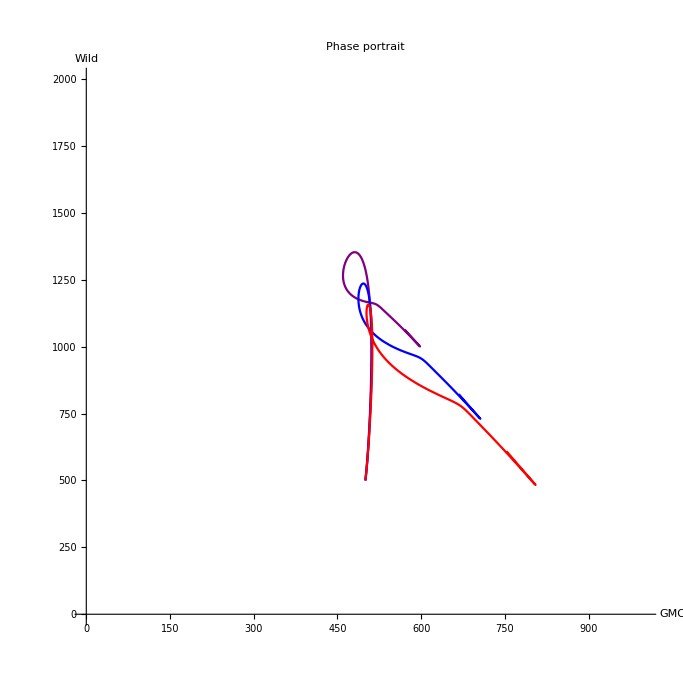

```mathematica
solt10=f[.4,.1,.1,.01,.95,7,0.001];
solt11=f[.4,.5,.1,.01,.95,7,0.001];
solt12=f[.4,.8,.1,.01,.95,7,0.001];
Plot[{solt10[[1]],solt11[[1]],solt12[[1]],solt10[[3]],solt11[[3]],solt12[[3]]},{t,0,200},PlotStyle->{Purple,Magenta,Pink,Brown,Orange,Yellow},PlotLabels->{"Low Beta", "Medium Beta", "High Beta","Low Beta", "Medium Beta", "High Beta"}, PlotLabel->"GMO population with Different competition of GMO on Wildtype",AxesLabel -> {"t", "N"}]
Show[ParametricPlot[{{solt10[[1]],solt10[[3]]},{solt11[[1]],solt11[[3]]},{solt12[[1]],solt12[[3]]}},{t,0,200},PlotRange->{{0,1000},{0,2000}},PlotStyle->{Purple,Blue,Red},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"GMO","Wild"}],StreamPlot [{GMO,Wild},{G,0,20},{B,0,4},StreamScale->{Tiny,Automatic,10}, StreamStyle->Pink]]
```

What these plot can tell is that our bacteria will survive

```mathematica
solb[bp_]:=f[.2,bp,.1,.01,.95,12,0.001]/.t->150;
sola[ap_]:=f[ap,.5,.1,.01,.95,12,0.001]/.t->150;
plot1=Plot[{solb[bp][[1]],solb[bp][[3]]},{bp,.1,1},PlotLabel->"Bifurcation plot for competition",PlotStyle->{Magenta,Pink},PlotLabels->{"GMO-plant (Beta)","WT-plant (Beta)"},Frame->{True,True,False,False},FrameLabel->{"Competition Coefficient","Population after 150 days"}]
plot2=Plot[{sola[ap][[1]],sola[ap][[3]]},{ap,.1,1},PlotLabel->"competition ",PlotStyle->{Purple,Red},PlotLabels->{"GMO-plant (Alpha)","WT-plant(Alpha)"},Frame->{True,True,False,False}(*,FrameLabel->{"Competition Coefficient (Alpha)","Population after 150 days"}*)]
Show[plot1,plot2,PlotRange->{0,1200}]
```

-Graphics-

-Graphics-

-Graphics-

### Patch Transfer

the patch transfer represent the bacteria migrating to and from the plant. there are three different paramters for these

#### Passive diffusion away from plant

this is the diffusion rate away from the plant

```mathematica
soldi[dp_]:=f[.4,.5,.1,dp,.95,7,0.001]/.t->150;
soldi1[dp_]:=f[.4,.5,.1,dp,.95,7,0.001]/.t->90;
Plot[{soldi[dp][[1]],soldi[dp][[2]],soldi[dp][[3]],soldi[dp][[4]]},{dp,.001,1},Frame->{True,True,False,False},FrameLabel->{"Passive diffusion coefficient","Population"},PlotLabel->"passive diffusion away from plant (t=150)",PlotStyle->{Purple,Blue, Green,Yellow},PlotLabels->{"GMO-plant","GMO-soil","WT-plant","WT-soil"}]
Plot[{soldi1[dp][[1]],soldi1[dp][[2]],soldi1[dp][[3]],soldi1[dp][[4]]},{dp,.001,1},Frame->{True,True,False,False},FrameLabel->{"Passive diffusion coefficient","Population"},PlotLabel->"passive diffusion away from plant (t=100)",PlotStyle->{Purple,Blue, Green,Yellow},PlotLabels->{"GMO-plant","GMO-soil","WT-plant","WT-soil"}]
```

-Graphics-

-Graphics-

if you plot the whole population you’ll get:

-Graphics-

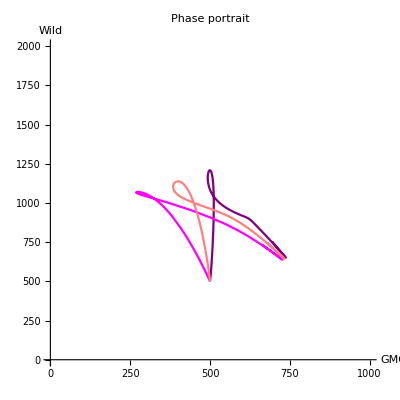

```mathematica
solt13=f[.4,.6,.1,.01,.95,7,0.001];
solt14=f[.4,.6,.1,.1,.95,7,0.001];
solt15=f[.4,.6,.1,.05,.95,7,0.001];
Plot[{solt13[[1]],solt14[[1]],solt15[[1]]},{t,0,200},PlotStyle->{Purple,Magenta,Pink},PlotLabels->{"0.01", "0.1", "0.4"}, PlotLabel->"Different passive diffusion rates away from the plant",AxesLabel -> {"t", "N"}]
Show[ParametricPlot[{{solt13[[1]],solt13[[3]]},{solt14[[1]],solt14[[3]]},{solt15[[1]],solt15[[3]]}},{t,0,200},PlotRange->{{0,1000},{0,2000}},PlotStyle->{Purple,Magenta,Pink},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"GMO","Wild"}],StreamPlot [{GMO,Wild},{G,0,20},{B,0,4},StreamScale->{Tiny,Automatic,10}, StreamStyle->Pink]]
```

#### Passive diffusion towards the plant

this is the diffusion rate towards the plant

```mathematica
solda1[d1p_]:=f[.4,.5,d1p,.01,.95,7,0.01]/.t->150;
solda2[d1p_]:=f[.4,.5,d1p,.01,.95,7,0.01]/.t->30;
Plot[{solda1[d1p][[1]],solda1[d1p][[2]],solda1[d1p][[3]],solda1[d1p][[4]]},{d1p,.001,1},Frame->{True,True,False,False},FrameLabel->{"Diffusion coefficient","Population"}, PlotLabel->"Diffusion to the plant(t=150)",PlotStyle->{Purple,Blue, Green,Yellow},PlotLabels->{"GMO-plant","GMO-soil","WT-plant","WT-soil"},PlotRange-> {0,3000}]
Plot[{solda2[d1p][[1]],solda2[d1p][[2]],solda2[d1p][[3]],solda2[d1p][[4]]},{d1p,.001,1},Frame->{True,True,False,False},FrameLabel->{"Diffusion coefficient","Population"},PlotLabel->"Diffusion to the plant(t=30)",PlotStyle->{Red, Orange, Green, Yellow},PlotLabels->{"GMO-plant","GMO-soil","WT-plant","WT-soil"}]
```

-Graphics-

-Graphics-

phaseplot and parametric plot

-Graphics-

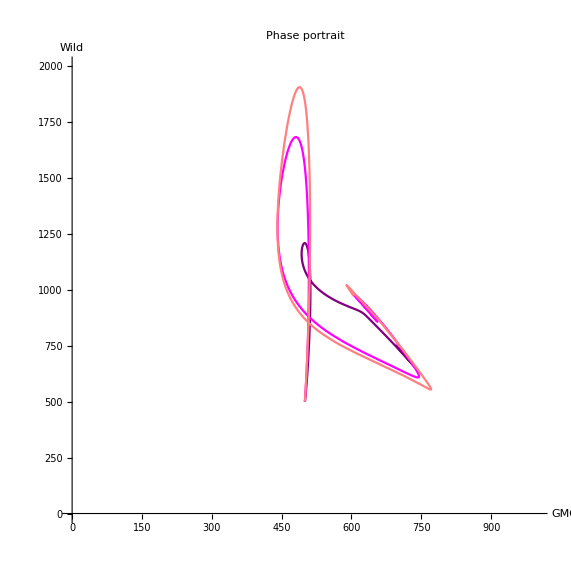

```mathematica
solt16=f[.4,.6,.1,.01,.95,7,0.001];
solt17=f[.4,.6,.4,.01,.95,7,0.001];
solt18=f[.4,.6,.8,.01,.95,7,0.001];
Plot[{solt16[[1]],solt17[[1]],solt18[[1]]},{t,0,200},PlotStyle->{Purple,Magenta,Pink,Brown,Orange,Yellow},PlotLabels->{"0.1", "0.4", "0.8"}, PlotLabel->"Different diffusion rates towards plant",AxesLabel -> {"t", "N"}]
Show[ParametricPlot[{{solt16[[1]],solt16[[3]]},{solt17[[1]],solt17[[3]]},{solt18[[1]],solt18[[3]]}},{t,0,200},PlotRange->{{0,1000},{0,2000}},PlotStyle->{Purple,Magenta,Pink},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"GMO","Wild"}],StreamPlot [{GMO,Wild},{G,0,20},{B,0,4},StreamScale->{Tiny,Automatic,10}, StreamStyle->Pink]]
```

#### Active Diffusion away from plant

this is active

```mathematica
solss[sp_]:=f[.6,.5,.01,0.01,.95,7,sp]/.t->150;
solsss[sp_]:=f[.6,.5,.01,0.01,.95,7,sp]/.t->150;
Plot[{solss[sp][[1]],solss[sp][[2]],solss[sp][[3]]},{sp,.001,.9},Frame->{True,True,False,False},FrameLabel->{Style["active diffusion coefficient ",FontSize->18],Style["Population",FontSize->18]},PlotLabel->Style["Bifurcation plot of the active diffusion away from the root",FontSize-> 20],FrameTicksStyle->Directive[FontSize->16],PlotStyle->{Purple,Blue, Green,Orange},PlotLabels->{Style["GMOp    ",FontSize->13],Style["GMOs    ",FontSize->13], Style["WTp    ",FontSize->13],Style["WTs    ",FontSize->13]}]


Plot[{solsss[sp][[1]],solsss[sp][[2]],solsss[sp][[3]],solsss[sp][[4]]},{sp,.001,0.9},Frame->{True,True,False,False},FrameLabel->{"Active Diffusion coefficient","Population"},PlotLabel->"active diffusion away from plant(t=150)",PlotStyle->{Purple,Blue, Green, Yellow},PlotLabels->{"GMO-plant","GMO-soil","WT-plant","WT-soil"}]
```

-Graphics-

-Graphics-

other plots

-Graphics-

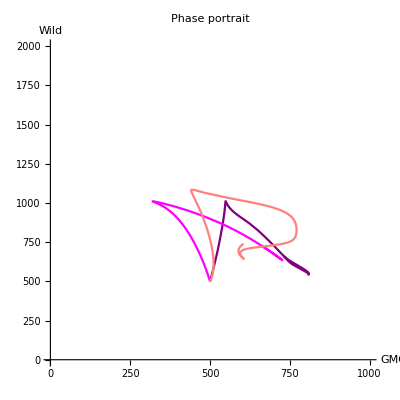

```mathematica
solt19=f[.4,.6,.1,.01,.91,7,0.01];
solt20=f[.4,.6,.1,.01,.95,7,0.1];
solt21=f[.4,.6,.1,.01,.95,7,0.05];
Plot[{solt19[[1]],solt20[[1]],solt21[[1]]},{t,0,200},PlotStyle->{Purple,Magenta,Pink},PlotLabels->{"0.01", "0.1", "0.4"}, PlotLabel->"Different Active diffusion rates away from the plant",AxesLabel -> {"t", "N"}]
Show[ParametricPlot[{{solt19[[1]],solt19[[3]]},{solt20[[1]],solt20[[3]]},{solt18[[1]],solt21[[3]]}},{t,0,200},PlotRange->{{0,1000},{0,2000}},PlotStyle->{Purple,Magenta,Pink},AspectRatio->1,PlotLabel->"Phase portrait", AxesLabel->{"GMO","Wild"}],StreamPlot [{GMO,Wild},{G,0,20},{B,0,4},StreamScale->{Tiny,Automatic,10}, StreamStyle->Pink]]
```

## Conclusion/Discusson

when making the model we made some assumptions, while also trying to get as close to the truth.  
In our model we observed that the initial amount of the population only matters in the time it will take to grow to the full population, but doesnot change the end population in numbers.
If the water activity gets below the minimal water activity, the population will decline, so it is important to make sure there is enough wateractivity in the potatofield. 
with temperature, only the growth will decline and the population will not go extinct if temperatures drop below the minimum temperature.
we can also see this when the minimum water activity rises above the water-activity in the soil.
within the minimum temperature range of our bacteria, our population is going to survive in the soil in the Netherlands.

The diffusion towards the plant only impacts on the number of wild type bacteria in the soil, and not much the GMO.
if the diffision toward the plant is really high then there will be more competition so that is not good for out GMO
If more than 1% of the population leaves the plant (passive diffusion) the population will not survive.
for the active diffusion the coefficent should not be more than 0.15 or our population is not going to be sufficient enough.

the competition between the bacteria might be one of the most important factors in order for our bacteria to survive. this depends of the competition form the GMO and towards the GMO.  competition is more sensitive on the GMO than on the wildtype.